# Black hole perturbation theory: Regge-Wheeler and Zerilli equations

## Presented by: Reggie Bernardo The 2nd Gravity Workshop PH (2020)

This is based on the Mathematica notebook of Chakrabarti, Steinhoff, and Rocha which is publicly available on Prof. Cardoso’s webpage: https://centra.tecnico.ulisboa.pt/network/grit/files/ringdown/.

Classic papers on the subject are
[1] Regge, T. and Wheeler, J.A., 1957. Stability of a Schwarzschild singularity. Physical Review, 108(4), p.1063.
[2] Zerilli, F.J., 1970. Effective potential for even-parity Regge-Wheeler gravitational perturbation equations. Physical Review Letters, 24(13), p.737.

More modern and stable language are used in
[3] Martel, K. and Poisson, E., 2005. Gravitational perturbations of the Schwarzschild spacetime: A practical covariant and gauge-invariant formalism. Physical Review D, 71(10), p.104003.
[4] Nagar, A. and Rezzolla, L., 2005. Gauge-invariant non-spherical metric perturbations of Schwarzschild black-hole spacetimes. Classical and Quantum Gravity, 22(16), p.R167.

## Black hole perturbation theory + xCoba

In this lecture, we shall derive the Regge-Wheeler and Zerilli equations in a Schwarzschild-(anti) de Sitter spacetime. These are the master equations that describe all of the gravitational perturbations on black holes in general relativity (GR). We follow the classic papers by Regge-Wheeler and Zerilli [1,2].

To aid our calculations, we employ xCoba (a companion to the xTensor package for component calculations). Specifically, we exploit xCoba to very efficiently compute the components of the perturbed Einstein equation.

```mathematica
(*import xCoba*)
<<xAct`xCoba`;

(*aesthetics*)
$PrePrint=ScreenDollarIndices;
$DefInfoQ=False;
$CVVerbose=False;
$CovDFormat="Prefix";
$epsilonSign=1;
$RicciSign=1;
$RiemannSign=1;

(*typical xAct starting point: define manifold and metric*)
dim=4;
DefManifold[Md,dim,{a,b,c,d,i,j,k,u,v,w,x,y,z}];
DefMetric[-1,g[-a,-b],CD,{";","▽"}];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

As in any xCoba sessions, we then define the chart “Schw” with coordinates (t_,r,θ,ϕ) in the manifold Md.

```mathematica
DefChart[Schw,Md,{0,1,2,3},{t[],r[],θ[],ϕ[]}];
```

Before defining the perturbed spacetime, here are a two more definitions that will aid us in our calculations. First, we define the function “linearize” which series expands an expression in terms of the perturbation parameter ϵ and then organizes the result.

```mathematica
DefConstantSymbol[ϵ];
linearize[expr_]:=Collect[Series[expr,{ϵ,0,1}]//Normal,ϵ,Together]
```

Second (and last), we define the spherical harmonics Y_lm (see Arfken 7th ed. page 757).

```mathematica
DefConstantSymbol/@{l,m,ω};
DefScalarFunction[PL,PrintAs->"P_lm"];

(*associated Legendre polynomials*)
PL''[θ_]:=-(l(l+1)-m^2 Csc[θ]^2) PL[θ]-Cot[θ]PL'[θ];

(*spherical harmonics*)
YLM:=(√((2l+1)/(4π)((l-m)!)/((l+m)!))E^(-I m ϕ[])PL[θ[]])E^(-I ω t[]);

(*for coloring the output*)
ColorOut[expr_]:=Style[expr//ScreenDollarIndices,FontColor->RGBColor[1/2,1,1/2]]
```

### Exercises

1. Linearize the following functions:
	(a) sin(ϵ x)
	(b) cos(ϵ x)
	(c) 1/(1-ϵ x)
	(d) exp(-ϵ x^2)
	
2. Use P_lm(θ)=LegendreP(l,m,Cos(θ)) and prove the following identities for {(l,m),(0,0),(1,0),(1,-1),(1,1),(2,0),(2,-1),(2,-2),(2,1),(2,2)}:

	(a) (∫_0)^π(P_lm(cos(θ)))^2 ⅆΩ=(2(2π))/(2l+1)
	(b) (∫_0)^π P_lm'(cos(θ))^2 ⅆΩ=((2π)2l(l+1))/(2l+1)
	
where dΩ=2π sin(θ)dθ.

## Background + perturbations

We are now ready to setup the background metric and, later on, its perturbations (in Regge-Wheeler gauge).

```mathematica
DefScalarFunction/@{h,f};
DefConstantSymbol/@{M,Λ};

(*general static and spherically symmetric background*)
background=DiagonalMatrix[{-h[r[]],1/f[r[]],r[]^2,r[]^2 Sin[θ[]]^2}];
"g_ab"==(background//MatrixForm)//ColorOut
```

g_ab==(-h[r] | 0 | 0 | 0
0 | 1/f[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Note that we are keeping the background general for the most part. In this way, we obtain more compact expressions and, eventually, a more powerful result.

The following rule can be used at the end of the calculation to turn the background to the Schwarzschild-(anti) de Sitter black hole.

```mathematica
SdS={h->Function[r,1-(2M)/r-(Λ r^2)/3],f->Function[r,1-(2M)/r-(Λ r^2)/3]};
```

### Gravitational perturbations

As is well-known, the analysis of metric perturbations can be decomposed into odd and even sectors as done by Regge-Wheeler back in 1957. The advantage of this analysis plus the decomposition into spherical harmonics is that the resulting modes can be studied independently with respect to the rest of the modes.

The even parity perturbations (four functions) in the Regge-Wheeler gauge are...

```mathematica
DefScalarFunction[H0,PrintAs->"H_0"];
DefScalarFunction[H1,PrintAs->"H_1"];
DefScalarFunction[H2,PrintAs->"H_2"];
DefScalarFunction[KK,PrintAs->"K"];
even=YLM{{h[r[]]H0[r[]],H1[r[]],0,0},{H1[r[]],H2[r[]]/f[r[]],0,0},{0,0,KK[r[]] r[]^2,0},{0,0,0,KK[r[]] r[]^2 Sin[θ[]]^2}};
"h_ab"==(even//MatrixForm)//ColorOut
```

h_ab==((ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) h[r] H_0[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) H_1[r] P_lm[θ])/(2 √π) | 0 | 0
(ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) H_1[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) H_2[r] P_lm[θ])/(2 √π f[r]) | 0 | 0
0 | 0 | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) K[r] P_lm[θ] r^2)/(2 √π) | 0
0 | 0 | 0 | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) K[r] P_lm[θ] r^2 Sin[θ]^2)/(2 √π))

...while the odd parity perturbations (two functions) are...

```mathematica
DefScalarFunction[h0,PrintAs->"h_0"];
DefScalarFunction[h1,PrintAs->"h_1"];odd={{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h0[r[]],Sin[θ[]]D[YLM,θ[]]h0[r[]]},{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h1[r[]],Sin[θ[]]D[YLM,θ[]]h1[r[]]},{-D[YLM,ϕ[]]/Sin[θ[]]h0[r[]],-D[YLM,ϕ[]]/Sin[θ[]]h1[r[]],0,0},{Sin[θ[]]D[YLM,θ[]]h0[r[]],Sin[θ[]]D[YLM,θ[]]h1[r[]],0,0}};
"h_ab"==(odd//MatrixForm)//ColorOut
```

h_ab==(0 | 0 | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] Sin[θ] P_lm'[θ])/(2 √π)
0 | 0 | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] Sin[θ] P_lm'[θ])/(2 √π)
(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π) | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π) | 0 | 0
(ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] Sin[θ] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] Sin[θ] P_lm'[θ])/(2 √π) | 0 | 0)

### Perturbed metric

Finally, we define the perturbed metric which we then input into xCoba for computing the components of the Einstein equation.

```mathematica
(*define η for bookkeeping odd sector*)
DefConstantSymbol[η];
metric=background+ϵ(even+η odd);

(*tell xCoba to compute curvature components*)
MetricInBasis[g,-Schw,metric];
MetricCompute[g,Schw,All,CVSimplify->linearize];
```

At this point, we can very easily compute all curvature quantities associated with the perturbed metric. For example, the unperturbed Ricci scalar is...

```mathematica
"R"==(RicciScalarCD[]//ToBasis[Schw]//ToValues//ToValues)/.ϵ->0//Simplification//ColorOut
```

R==1/(2 h[r]^2 r^2)(-4 h[r]^2 (-1+f[r]+r f'[r])+f[r] r^2 h'[r]^2-h[r] r (r f'[r] h'[r]+2 f[r] (2 h'[r]+r h''[r])))

### Exercises

3. Show that the event horizon and cosmological horizon i.e., h(r_H)=f(r_H)=0, of the Schwazschild de Sitter spacetime are given by

	r_EH=(Λ-ⅈ √3 Λ+(1+ⅈ √3) (3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3))/(2 Λ (3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3))
	
	r_CH=(Λ-ⅈ √3 Λ+(1+ⅈ √3) (3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3))/(2 Λ (3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3))

4. Evaluate the Ricci and Kretschmann scalars for the Schwarzschild-de Sitter metric.

5. Show that the Schwarzschild-de Sitter metric is an exact solution to the field equation: G_ab+Λ g_ab=0.

## Einstein equation

The field equations for the metric is, of course, the Einstein equation given by...

```mathematica
EE=(RicciCD[-c,-b]-1/2 g[-c,-b]RicciScalarCD[])+Λ g[-c,-b];
EE=="8 π T_cb"//ColorOut
```

Λ g |   |  
c | b+R[▽] |   |  
c | b-1/2 g |   |  
c | b R[▽]==8 π T_cb

Note that we have included a cosmological constant Λ since we are interested in general in perturbations of the Schwarzschild-(anti) de Sitter black hole.

The components of the left hand side can be accessed as follows.

```mathematica
removebrackets={t[]->t,r[]->r,θ[]->θ,ϕ[]->ϕ};
EERW=(EE//ToBasis[Schw]//ComponentArray//ToValues//ToValues)/.removebrackets//linearize;
```

### Matter sector

To proceed, we move on to the matter sector of the theory and decompose the stress-energy tensor (SET) into spherical harmonics.

Here are the ten perturbations that we shall associate with the stress-energy tensor.

```mathematica
(*odd sector*)
DefScalarFunction[tt0,PrintAs->"t_0"];
DefScalarFunction[tt1,PrintAs->"t_1"];
DefScalarFunction[tt2,PrintAs->"t_2"];

(*even sector*)
DefScalarFunction[T0,PrintAs->"T_0"];
DefScalarFunction[T1,PrintAs->"T_1"];
DefScalarFunction[T2,PrintAs->"T_2"];
DefScalarFunction[TK,PrintAs->"T_K"];
DefScalarFunction[t0,PrintAs->"𝓉_0"];
DefScalarFunction[t1,PrintAs->"𝓉_1"];
DefScalarFunction[TG,PrintAs->"T_G"];
```

The even parity SET is...

```mathematica
SETeven=ϵ{{h[r[]]T0[r[]]YLM,T1[r[]]YLM,t0[r[]] D[YLM,θ[]],t0[r[]] D[YLM,ϕ[]]},{T1[r[]]YLM,T2[r[]]/f[r[]] YLM,t1[r[]] D[YLM,θ[]],t1[r[]] D[YLM,ϕ[]]},{t0[r[]] D[YLM,θ[]],t1[r[]] D[YLM,θ[]],r[]^2(TK[r[]]YLM+TG[r[]]D[YLM,{θ[],2}]),r[]^2 TG[r[]](D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]] D[YLM,ϕ[]])},{t0[r[]] D[YLM,ϕ[]],t1[r[]] D[YLM,ϕ[]],r[]^2 TG[r[]](D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]] D[YLM,ϕ[]]),r[]^2(TK[r[]] Sin[θ[]]^2 YLM+TG[r[]](D[YLM,{ϕ[],2}]+Sin[θ[]]Cos[θ[]]D[YLM,θ[]]))}};
PFevenRW=SETeven/.removebrackets//linearize;
"T_ab"==(PFevenRW//MatrixForm)//ColorOut
```

T_ab==((ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h[r] P_lm[θ] T_0[r])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] T_1[r])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) 𝓉_0[r] P_lm'[θ])/(2 √π) | -(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] 𝓉_0[r])/(2 √π)
(ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] T_1[r])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] T_2[r])/(2 √π f[r]) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) 𝓉_1[r] P_lm'[θ])/(2 √π) | -(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] 𝓉_1[r])/(2 √π)
(ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) 𝓉_0[r] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) 𝓉_1[r] P_lm'[θ])/(2 √π) | -(ⅇ^(-ⅈ m ϕ-ⅈ t ω) r^2 ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (l P_lm[θ] T_G[r]+l^2 P_lm[θ] T_G[r]-m^2 Csc[θ]^2 P_lm[θ] T_G[r]-P_lm[θ] T_K[r]+Cot[θ] T_G[r] P_lm'[θ]))/(2 √π) | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m r^2 ϵ √(((1+2 l) (l-m)!)/((l+m)!)) T_G[r] (Cot[θ] P_lm[θ]-P_lm'[θ]))/(2 √π)
-(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] 𝓉_0[r])/(2 √π) | -(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] 𝓉_1[r])/(2 √π) | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m r^2 ϵ √(((1+2 l) (l-m)!)/((l+m)!)) T_G[r] (Cot[θ] P_lm[θ]-P_lm'[θ]))/(2 √π) | -(ⅇ^(-ⅈ m ϕ-ⅈ t ω) r^2 ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (m^2 P_lm[θ] T_G[r]-P_lm[θ] Sin[θ]^2 T_K[r]-Cos[θ] Sin[θ] T_G[r] P_lm'[θ]))/(2 √π))

...and the odd parity SET is...

```mathematica
PFodd=ϵ{{0,0,(-tt0[r[]])/Sin[θ[]] D[YLM,ϕ[]],tt0[r[]]Sin[θ[]] D[YLM,θ[]]},{0,0,(-tt1[r[]])/Sin[θ[]] D[YLM,ϕ[]],tt1[r[]]Sin[θ[]] D[YLM,θ[]]},{(-tt0[r[]])/Sin[θ[]] D[YLM,ϕ[]],(-tt1[r[]])/Sin[θ[]] D[YLM,ϕ[]],tt2[r[]](1/Sin[θ[]] D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]]^2 D[YLM,ϕ[]]),1/2 tt2[r[]](1/Sin[θ[]] D[YLM,{ϕ[],2}]+Cos[θ[]]D[YLM,θ[]]-Sin[θ[]]D[YLM,{θ[],2}])},{tt0[r[]]Sin[θ[]] D[YLM,θ[]],tt1[r[]]Sin[θ[]]D[YLM,θ[]],1/2 tt2[r[]](1/Sin[θ[]] D[YLM,{ϕ[],2}]+Cos[θ[]]D[YLM,θ[]]-Sin[θ[]]D[YLM,{θ[],2}]),-tt2[r[]](Sin[θ[]]D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]D[YLM,ϕ[]])}};
PFoddRW=PFodd/.removebrackets//linearize;
"T_ab"==(PFoddRW//MatrixForm)//ColorOut
```

T_ab==(0 | 0 | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] t_0[r])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] t_0[r] P_lm'[θ])/(2 √π)
0 | 0 | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] t_1[r])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] t_1[r] P_lm'[θ])/(2 √π)
(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] t_0[r])/(2 √π) | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] t_1[r])/(2 √π) | (ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) t_2[r] (Cot[θ] P_lm[θ]-P_lm'[θ]))/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) t_2[r] (-2 m^2 P_lm[θ]+l P_lm[θ] Sin[θ]^2+l^2 P_lm[θ] Sin[θ]^2+2 Cos[θ] Sin[θ] P_lm'[θ]))/(4 √π)
(ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] t_0[r] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] t_1[r] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ m ϕ-ⅈ t ω) ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) t_2[r] (-2 m^2 P_lm[θ]+l P_lm[θ] Sin[θ]^2+l^2 P_lm[θ] Sin[θ]^2+2 Cos[θ] Sin[θ] P_lm'[θ]))/(4 √π) | -(ⅈ ⅇ^(-ⅈ m ϕ-ⅈ t ω) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) t_2[r] (Cos[θ] P_lm[θ]-Sin[θ] P_lm'[θ]))/(2 √π))

### Exercises

6. Obtain the O(ϵ^0) terms of EE and show that all components would vanish with SdS.

7. [Monopole] Simplify the even and odd parity T_ab for l=0 and m=0. How many independent components are there?

8. [Dipole] Simplify the even and odd parity T_ab for l=1 and m=0. How many independent components are there?

## Odd parity sector

In this section, we derive the master equation governing the odd parity gravitational perturbations.

To start, we print the odd parity pieces (h_0, h_1) of the Einstein field equation.

```mathematica
EERWodd=Coefficient[EERW,η,1];

(*this solve for h0[r] from the θφ-component*)
h0sol=h0[r]/.Solve[EERWodd[[3,4]]==8π PFoddRW[[3,4]],h0[r]][[1]]//FullSimplify;
"h_0(r)"==h0sol//ColorOut
```

h_0(r)==(ⅈ (f[r] h_1[r] h'[r]+h[r] (16 π t_2[r]+h_1[r] f'[r]+2 f[r] h_1'[r])))/(2 ω)

All h_0 in the field equations may now be replaced by this functional expression h_0[h_1]. The odd parity field equations then become...

```mathematica
EERWodd2=EERWodd/.h0->Function[r,h0sol//Evaluate];
```

We can extract the master equation from the rφ-component:

```mathematica
h1ppsol=h1''[r]/.Solve[EERWodd2[[2,4]]==8π PFoddRW[[2,4]],h1''[r]][[1]]//FullSimplify;
"h_1''(r)"==h1ppsol//ColorOut
```

h_1''(r)==-1/(2 r^2 f[r] h[r]^2)(r^2 f[r] h_1[r] h'[r]^2+h[r]^2 (r (32 π r t_1[r]+(-4 f[r]+3 r f'[r]) h_1'[r]+16 π (-2 t_2[r]+r t_2'[r]))+h_1[r] (-2 (-2+l+l^2+2 r^2 Λ+2 r f'[r])+r^2 f''[r]))+r h[r] (r h'[r] (16 π t_2[r]+3 f[r] h_1'[r])+h_1[r] (2 r ω^2+(-4 f[r]+r f'[r]) h'[r]-r f[r] h''[r])))

This is, in principle, already the master equation for the odd parity perturbations. It is, however, more conventional (and pedagogical!) to write this down in a form that looks like the Schrodinger equation. The first step to this is to define the Regge-Wheeler (RW) master function Q. Then, the master equation becomes...

```mathematica
RWfunc=h1->Function[r,r/(√(h[r]f[r])) Q[r]];
MasterOdd=(h1''[r]-h1ppsol/.RWfunc//Simplify)==0;
```

To put the master equation in Schrodinger equation form, we also define the tortoise coordinate r_*(r):

```mathematica
DefScalarFunction[rT,PrintAs->"r_*"];
rTdef={rT'[r]->1/(√(h[r]f[r])),rT''[r]-> D[1/(√(h[r]f[r])),r]};
```

The master equation becomes...

```mathematica
MasterOdd2=MasterOdd/.{Q->Function[r,Q[rT[r]]],tt1->Function[r,tt1[rT[r]]],tt2->Function[r,tt2[rT[r]]]}/.rTdef//Simplify;
```

Finally, we normalize the coefficient in front of the second derivative to obtain...

```mathematica
normQpp=Coefficient[MasterOdd2//First,Q''[rT[r]]];
MasterOdd3=Collect[(MasterOdd2//First)/normQpp//Simplify,{Q[rT[r]],Q''[rT[r]]}]==0;
```

We shall clean further the master equation by defining the potential V_odd and putting all source terms to the right hand side and calling them S_odd.

```mathematica
Sodd=(-MasterOdd3//First)/.{Q[rT[r]]->0,Q''[rT[r]]->0}//Simplify;
Vodd=-(Coefficient[MasterOdd3//First,Q[rT[r]]]-ω^2)//Simplify;
```

The Regge-Wheeler equation is given by...

```mathematica
RWeq=Q''[rT[r]]+(ω^2-Vodd)Q[rT[r]]==Sodd;
RWeq//ColorOut
```

Q[r_*[r]] (ω^2-1/(2 r^2 h[r])(h[r]^2 (2 (-2+l+l^2+2 r^2 Λ)+4 f[r]+r f'[r])-r^2 f[r] h'[r]^2+r h[r] (r f'[r] h'[r]+f[r] (h'[r]+2 r h''[r]))))+Q''[r_*[r]]==-1/(r^2 √(f[r] h[r]))8 π h[r] (f[r] (2 h[r] (r t_1[r_*[r]]-t_2[r_*[r]])+r t_2[r_*[r]] h'[r])+r √(f[r] h[r]) t_2'[r_*[r]])

It is easy to verify that this is the same as MasterOdd3, e.g.,

```mathematica
((MasterOdd3//First)-(RWeq//First)//Simplify)==-Sodd//ColorOut
```

True

## Even parity sector

In this section, we derive the even parity master equation. The main idea proceeds in the same way as in the odd parity sector, i.e., we uncouple the differential equation for the perturbation components.

The challenge for the even parity sector, compared to the odd parity sector, is having to deal with four perturbation functions. Nonetheless, the extraction of the master equation is efficiently manageable with Mathematica.

To start, we print the even parity pieces (H_0, H_1, H_2, K) of the Einstein field equation.

```mathematica
EERWeven=ϵ Coefficient[EERW/.η->0,ϵ,1]//Simplify;
```

The easiest piece to deal with is the φθ piece. From this, we can obtain the functional expression H_2[H_0]:

```mathematica
H2sol=H2[r]/.Solve[EERWeven[[3,4]]==8π PFevenRW[[3,4]],H2[r]][[1]];
H2[r_]:=H2sol//Evaluate

"H_2(r)"==H2[r]//ColorOut
```

H_2(r)==H_0[r]-16 π r^2 T_G[r]

We are then down to three perturbations. To uncouple these, we first resort to looking at the tθ, tr, and rθ components:

```mathematica
eq0=Solve[{EERWeven[[1,3]]==8π PFevenRW[[1,3]],EERWeven[[1,2]]==8π PFevenRW[[1,2]],EERWeven[[2,3]]==8π PFevenRW[[2,3]]},{H0'[r],H1'[r],KK'[r]}][[1]]//Simplify;

"H_0'(r)"==H0'[r]/.eq0//ColorOut
"H_1'(r)"==H1'[r]/.eq0//ColorOut
"K'(r)"==KK'[r]/.eq0//ColorOut
```

H_0'(r)==1/(2 r^2 ω h[r])(h[r] (2 r ω H_0[r]+2 r (-ω K[r]+16 π r ω 𝓉_1[r]-8 ⅈ π r T_1[r])+ⅈ H_1[r] (-2+l+l^2+2 r^2 Λ+2 f[r]+2 r f'[r]))+r^2 ω (-2 ⅈ ω H_1[r]+(-2 H_0[r]+K[r]+16 π r^2 T_G[r]) h'[r]))

H_1'(r)==1/(2 f[r] h[r])(h[r] (-2 ⅈ ω H_0[r]-2 ⅈ ω K[r]+32 π 𝓉_0[r]+32 ⅈ π r^2 ω T_G[r]-H_1[r] f'[r])-f[r] H_1[r] h'[r])

K'(r)==1/(2 r^2 ω h[r])(h[r] (2 r ω H_0[r]+ⅈ (2 ⅈ r (ω K[r]+8 π r (ⅈ T_1[r]+2 r ω T_G[r]))+H_1[r] (-2+l+l^2+2 r^2 Λ+2 f[r]+2 r f'[r])))+r^2 ω K[r] h'[r])

The power of these three expressions is to reduce any other independent expression of the perturbations into an algebraic expression. In particular, we shall use eq0 to reduce the rr component into an algebraic equation for H_0, H_1, and K:

```mathematica
rr=EERWeven[[2,2]]==8π PFevenRW[[2,2]]/.eq0;
```

From this algebraic expression, we obtain the functional H_0[H_1,K] given by...

```mathematica
H0sol=H0[r]/.Solve[rr,H0[r]][[1]]//Simplify;

"H_0(r)"==H0sol//ColorOut
```

H_0(r)==(2 ω h[r] ((-2 r^2 ω^2+(-2+l+l^2) h[r]) K[r]+16 π r^2 h[r] (T_2[r]+2 (-1+r^2 Λ) T_G[r]))-2 ⅈ f[r]^2 h[r] H_1[r] h'[r]+f[r] (64 π r ω h[r]^2 (𝓉_1[r]+r T_G[r])-r^2 ω K[r] h'[r]^2+h[r] (2 r (ω K[r]+8 π r (ⅈ T_1[r]+4 r ω T_G[r])) h'[r]-ⅈ H_1[r] (-4 r ω^2+(-2+l+l^2+2 r^2 Λ+2 r f'[r]) h'[r]))))/(2 ω h[r] ((-2+l+l^2+2 r^2 Λ) h[r]+3 r f[r] h'[r]))

This brings the analysis down to two perturbations.

```mathematica
eq1={H1'[r]-(H1'[r]/.eq0/.H0->Function[r,H0sol//Evaluate]//Simplify)==0,KK'[r]-(KK'[r]/.eq0/.H0->Function[r,H0sol//Evaluate]//Simplify)==0};
```

## Even parity sector

We made considerable progress in simplifying the even parity sector of the Einstein field equations down to eq1.

To proceed, let us first factor out an ω^-1 from H_1, i.e., R=H_1/ω.

```mathematica
eq2=eq1/.H1->Function[r,ω R[r]];

eq2[[1]]//ColorOut
eq2[[2]]//ColorOut
```

-1/(2 f[r] h[r])(-ω f[r] R[r] h'[r]+h[r] (-2 ⅈ ω K[r]+32 π 𝓉_0[r]+32 ⅈ π r^2 ω T_G[r]-ω R[r] f'[r]-(ⅈ (2 ω h[r] ((-2 r^2 ω^2+(-2+l+l^2) h[r]) K[r]+16 π r^2 h[r] (T_2[r]+2 (-1+r^2 Λ) T_G[r]))-2 ⅈ ω f[r]^2 h[r] R[r] h'[r]+f[r] (64 π r ω h[r]^2 (𝓉_1[r]+r T_G[r])-r^2 ω K[r] h'[r]^2+h[r] (2 r (ω K[r]+8 π r (ⅈ T_1[r]+4 r ω T_G[r])) h'[r]-ⅈ ω R[r] (-4 r ω^2+(-2+l+l^2+2 r^2 Λ+2 r f'[r]) h'[r])))))/(h[r] ((-2+l+l^2+2 r^2 Λ) h[r]+3 r f[r] h'[r]))))+ω R'[r]==0

-1/(2 r^2 ω h[r])(r^2 ω K[r] h'[r]+h[r] (ⅈ (2 ⅈ r (ω K[r]+8 π r (ⅈ T_1[r]+2 r ω T_G[r]))+ω R[r] (-2+l+l^2+2 r^2 Λ+2 f[r]+2 r f'[r]))+(r (2 ω h[r] ((-2 r^2 ω^2+(-2+l+l^2) h[r]) K[r]+16 π r^2 h[r] (T_2[r]+2 (-1+r^2 Λ) T_G[r]))-2 ⅈ ω f[r]^2 h[r] R[r] h'[r]+f[r] (64 π r ω h[r]^2 (𝓉_1[r]+r T_G[r])-r^2 ω K[r] h'[r]^2+h[r] (2 r (ω K[r]+8 π r (ⅈ T_1[r]+4 r ω T_G[r])) h'[r]-ⅈ ω R[r] (-4 r ω^2+(-2+l+l^2+2 r^2 Λ+2 r f'[r]) h'[r])))))/(h[r] ((-2+l+l^2+2 r^2 Λ) h[r]+3 r f[r] h'[r]))))+K'[r]==0

To uncouple these two equations, we define four free functions f_i and perturbations R̂ and K̂. The game then proceeds by finding the f_is such that the master equation takes the Schrodinger equation form.

```mathematica
(*define hatted functions*)
transform={KK->Function[r,f1[r]Kh[r]+f2[r]Rh[r]],R->Function[r,f3[r]Kh[r]+f4[r]Rh[r]]};

(*change independent variable to tortoise coordinate*)
TorTpert={Rh->Function[r,Rh[rT[r]]],Kh->Function[r,Kh[rT[r]]]};
TorTmatter={T1->Function[r,T1[rT[r]]],T2->Function[r,T2[rT[r]]],TG->Function[r,TG[rT[r]]],t1->Function[r,tt1[rT[r]]],t0->Function[r,tt0[rT[r]]]};

(*apply transformations*)
eq2transform=eq2/.transform/.TorTpert/.TorTmatter/.rTdef;
eq2sol=Solve[eq2transform,{Rh'[rT[r]],Kh'[rT[r]]}][[1]]//Simplify;

eq3={Rh'[rT[r]]-(Rh'[rT[r]]/.eq2sol)==0,Kh'[rT[r]]-(Kh'[rT[r]]/.eq2sol)==0};
```

The system (for f_is) is overdetermined. We exploit this by choosing f_2=1:

```mathematica
f2[r_]:=1
```

To find f_1, f_3, and f_4, we require two things. First, we want the functional dependence of ∂_(r*) K̂-R̂ on R̂ to completely vanish. Second, we want the functional dependence of ∂_(r*) R̂ on R̂ to completely vanish. The reason for this is so that ∂_(r*) (∂_(r*) K̂-R̂)=((∂_(r*))^2 K̂)-(∂_(r*) R̂)=F[(∂_(r*))^2 K̂,K̂]. Thus, we have a Schrodinger equation.

Formulating the requirements...

```mathematica
eq3sol=Solve[eq3,{Rh'[rT[r]],Kh'[rT[r]]}][[1]];

req1=Kh'[rT[r]]-Rh[rT[r]]/.eq3sol;
req2=Coefficient[Rh'[rT[r]]/.eq3sol,Rh[rT[r]]];
```

The functions f_is are solved as follows.

```mathematica
f4sol=f4[r]/.Solve[Coefficient[Coefficient[req1,Rh[rT[r]]],ω^2]==0,f4[r]][[1]]//Simplify;
f3sol=f3[r]/.Solve[Coefficient[req1/.f4->Function[r,f4sol//Evaluate],Rh[rT[r]]]==0,f3[r]][[1]]//Simplify;
f1sol=f1[r]/.Solve[(req2/.{f4->Function[r,f4sol//Evaluate],f3->Function[r,f3sol//Evaluate]})==0,f1[r]][[1]]//Simplify;

"f_4"==f4sol//ColorOut
"f_3"==f3sol//ColorOut
"f_1"==f1sol//ColorOut
```

f_4==-(ⅈ r)/f[r]

f_3==1/(2 f[r]^2 h[r])ⅈ (h[r] √(f[r] h[r]) (-2+l+l^2+2 r^2 Λ+r f'[r])+f[r] (-2 r f1[r] h[r]+2 r √(f[r] h[r]) h'[r]))

f_1==(h[r]^2 (2 (-2+l+l^2) f[r]+(-2+l+l^2+2 r^2 Λ) (-2+l+l^2+2 r^2 Λ+2 r f'[r]))+r f[r] h[r] (3 (-2+l+l^2+2 r^2 Λ)+4 r f'[r]) h'[r]+2 r^2 f[r]^2 h'[r]^2)/(2 r √(f[r] h[r]) ((-2+l+l^2+2 r^2 Λ) h[r]+3 r f[r] h'[r]))

These functions simplify req1 to a source term in S(A)dS spacetime (which vanishes in vacuum)...

```mathematica
f1[r_]:=f1sol//Evaluate;
f3[r_]:=f3sol//Evaluate;
f4[r_]:=f4sol//Evaluate;

Sreq1=req1//Simplify;

"req1"==Collect[Sreq1/.SdS,{Kh[rT[r]]},Simplify]//ColorOut
```

req1==(16 ⅈ π (6 M-3 r+r^3 Λ) (r T_1[r_*[r]]+2 t_0[r_*[r]]))/(3 (6 M+(-2+l+l^2) r) ω)

Simplifying the coupled equation eq3, we now have...

```mathematica
eq4=eq3sol//Simplify;
```

Comment on req1:

A key realization for proceeding along the lines given above is that ∂_(r*) K̂-R̂ is independent of K̂ for the static and stationary SAdS background. The following line shows this.

```mathematica
"∂"==req1/.SdS//Simplify//ColorOut
```

∂==(16 ⅈ π (6 M-3 r+r^3 Λ) (r T_1[r_*[r]]+2 t_0[r_*[r]]))/(3 (6 M+(-2+l+l^2) r) ω)

Outside of the SAdS background, req1 instead gives...

```mathematica
"∂"==Collect[req1,{Kh[rT[r]]},Simplify]//ColorOut
```

∂==-(16 ⅈ π f[r] h[r] (r T_1[r_*[r]]+2 t_0[r_*[r]]))/(ω (h[r] (-2+l+l^2+2 r^2 Λ+r f'[r])+2 r f[r] h'[r]))+(Kh[r_*[r]] ((-2+l+l^2+2 r^2 Λ) h[r]^3 f'[r] (-2+l+l^2+2 r^2 Λ+r f'[r])-f[r] h[r]^2 (((-2+l+l^2+2 r^2 Λ)^2-r (-2+l+l^2+2 r^2 Λ) f'[r]-2 r^2 f'[r]^2) h'[r]+h[r] ((-2+l+l^2+4 r^2 Λ) f'[r]+r (-2+l+l^2+2 r^2 Λ) (6 Λ+f''[r])))+2 r f[r]^3 h'[r] (r h'[r]^2-3 h[r] (2 h'[r]+r h''[r]))-f[r]^2 h[r] (2 r (-2+l+l^2+2 r^2 Λ+2 r f'[r]) h'[r]^2+h[r] (h'[r] (-10+5 l+5 l^2+26 r^2 Λ+6 r f'[r]+3 r^2 f''[r])+2 r (-2+l+l^2+2 r^2 Λ) h''[r]))))/(√(f[r] h[r]) (h[r] (-2+l+l^2+2 r^2 Λ+r f'[r])+2 r f[r] h'[r]) ((-2+l+l^2+2 r^2 Λ) h[r]+3 r f[r] h'[r]))

This is the reason for using both f_4 and f_3 to vanish the R̂ dependence of ∂_(r*) K̂-R̂.

## Even parity sector

In this slide, we finally derive the Zerilli master equation for the even parity perturbations.

```mathematica
ZEhf=Collect[Kh''[rT[r]]-(Rh'[rT[r]]/.eq4)-(√(f[r]h[r])D[Sreq1,r]/.rTdef),{Kh[rT[r]],Kh'[rT[r]],Kh''[rT[r]]},Simplify]==0;
```

The expression ZEhf which is a functional of h and f is very unwieldy. The Zerilli master equation is the limit of this when the background reduces to the Schwarzschild-(anti) de Sitter spacetime.

```mathematica
$Assumptions=r>0&&M>0&&1-(2M)/r-(Λ r^2)/3≥0;
MasterEven=Collect[ZEhf/.SdS,{Kh[rT[r]],Kh'[rT[r]],Kh''[rT[r]]},Simplify];
```

We simplify further by collecting the source terms and the potential.

```mathematica
(*collecting the source terms*)
Seven=(-MasterEven//First)/.{Kh[rT[r]]->0,Kh''[rT[r]]->0}//Simplify;

(*collecting the potential*)
Veven=-(Coefficient[MasterEven//First,Kh[rT[r]]]-ω^2)//Simplify;

"S_even"==Seven//ColorOut
"V_even"==Veven//ColorOut
```

S_even==(16 π (6 M-3 r+r^3 Λ) (-2 ⅈ r (18 M^2+(-2+l+l^2) r^4 Λ+3 M r (-4-l-l^2+4 r^2 Λ)) T_1[r_*[r]]-3 r^3 (6 M+(-2+l+l^2) r) ω T_2[r_*[r]]+108 M^2 r^2 ω T_G[r_*[r]]-72 M r^3 ω T_G[r_*[r]]+36 l M r^3 ω T_G[r_*[r]]+36 l^2 M r^3 ω T_G[r_*[r]]+12 r^4 ω T_G[r_*[r]]-12 l r^4 ω T_G[r_*[r]]-9 l^2 r^4 ω T_G[r_*[r]]+6 l^3 r^4 ω T_G[r_*[r]]+3 l^4 r^4 ω T_G[r_*[r]]-72 ⅈ M^2 t_0[r_*[r]]+48 ⅈ M r t_0[r_*[r]]-6 ⅈ l M r t_0[r_*[r]]-6 ⅈ l^2 M r t_0[r_*[r]]+6 ⅈ l r^2 t_0[r_*[r]]+3 ⅈ l^2 r^2 t_0[r_*[r]]-6 ⅈ l^3 r^2 t_0[r_*[r]]-3 ⅈ l^4 r^2 t_0[r_*[r]]-48 ⅈ M r^3 Λ t_0[r_*[r]]+8 ⅈ r^4 Λ t_0[r_*[r]]-4 ⅈ l r^4 Λ t_0[r_*[r]]-4 ⅈ l^2 r^4 Λ t_0[r_*[r]]+72 M^2 r ω t_1[r_*[r]]-60 M r^2 ω t_1[r_*[r]]+12 l M r^2 ω t_1[r_*[r]]+12 l^2 M r^2 ω t_1[r_*[r]]+12 r^3 ω t_1[r_*[r]]-6 l r^3 ω t_1[r_*[r]]-6 l^2 r^3 ω t_1[r_*[r]]+12 M r^4 Λ ω t_1[r_*[r]]-4 r^5 Λ ω t_1[r_*[r]]+2 l r^5 Λ ω t_1[r_*[r]]+2 l^2 r^5 Λ ω t_1[r_*[r]]+18 ⅈ M r^3 T_1'[r_*[r]]-6 ⅈ r^4 T_1'[r_*[r]]+3 ⅈ l r^4 T_1'[r_*[r]]+3 ⅈ l^2 r^4 T_1'[r_*[r]]+36 ⅈ M r^2 t_0'[r_*[r]]-12 ⅈ r^3 t_0'[r_*[r]]+6 ⅈ l r^3 t_0'[r_*[r]]+6 ⅈ l^2 r^3 t_0'[r_*[r]]))/(9 r^2 (6 M+(-2+l+l^2) r)^2 ω)

V_even==-((432 M^4+l (1+l) (-2+l+l^2)^2 r^4 (-3+r^2 Λ)-72 M^3 r (9-3 l-3 l^2+r^2 Λ)+6 (-2+l+l^2)^2 M r^3 (-3+l+l^2+r^2 Λ)-12 M^2 r^2 (-30-6 l^3-3 l^4+2 r^4 Λ^2-3 l (-7+r^2 Λ)-3 l^2 (-6+r^2 Λ)))/(3 r^4 (6 M+(-2+l+l^2) r)^2))

The Zerilli equation is given by...

```mathematica
ZE=Kh''[rT[r]]+(ω^2-Veven)Kh[rT[r]]==Seven;

ZE//ColorOut
```

((432 M^4+l (1+l) (-2+l+l^2)^2 r^4 (-3+r^2 Λ)-72 M^3 r (9-3 l-3 l^2+r^2 Λ)+6 (-2+l+l^2)^2 M r^3 (-3+l+l^2+r^2 Λ)-12 M^2 r^2 (-30-6 l^3-3 l^4+2 r^4 Λ^2-3 l (-7+r^2 Λ)-3 l^2 (-6+r^2 Λ)))/(3 r^4 (6 M+(-2+l+l^2) r)^2)+ω^2) Kh[r_*[r]]+Kh''[r_*[r]]==(16 π (6 M-3 r+r^3 Λ) (-2 ⅈ r (18 M^2+(-2+l+l^2) r^4 Λ+3 M r (-4-l-l^2+4 r^2 Λ)) T_1[r_*[r]]-3 r^3 (6 M+(-2+l+l^2) r) ω T_2[r_*[r]]+108 M^2 r^2 ω T_G[r_*[r]]-72 M r^3 ω T_G[r_*[r]]+36 l M r^3 ω T_G[r_*[r]]+36 l^2 M r^3 ω T_G[r_*[r]]+12 r^4 ω T_G[r_*[r]]-12 l r^4 ω T_G[r_*[r]]-9 l^2 r^4 ω T_G[r_*[r]]+6 l^3 r^4 ω T_G[r_*[r]]+3 l^4 r^4 ω T_G[r_*[r]]-72 ⅈ M^2 t_0[r_*[r]]+48 ⅈ M r t_0[r_*[r]]-6 ⅈ l M r t_0[r_*[r]]-6 ⅈ l^2 M r t_0[r_*[r]]+6 ⅈ l r^2 t_0[r_*[r]]+3 ⅈ l^2 r^2 t_0[r_*[r]]-6 ⅈ l^3 r^2 t_0[r_*[r]]-3 ⅈ l^4 r^2 t_0[r_*[r]]-48 ⅈ M r^3 Λ t_0[r_*[r]]+8 ⅈ r^4 Λ t_0[r_*[r]]-4 ⅈ l r^4 Λ t_0[r_*[r]]-4 ⅈ l^2 r^4 Λ t_0[r_*[r]]+72 M^2 r ω t_1[r_*[r]]-60 M r^2 ω t_1[r_*[r]]+12 l M r^2 ω t_1[r_*[r]]+12 l^2 M r^2 ω t_1[r_*[r]]+12 r^3 ω t_1[r_*[r]]-6 l r^3 ω t_1[r_*[r]]-6 l^2 r^3 ω t_1[r_*[r]]+12 M r^4 Λ ω t_1[r_*[r]]-4 r^5 Λ ω t_1[r_*[r]]+2 l r^5 Λ ω t_1[r_*[r]]+2 l^2 r^5 Λ ω t_1[r_*[r]]+18 ⅈ M r^3 T_1'[r_*[r]]-6 ⅈ r^4 T_1'[r_*[r]]+3 ⅈ l r^4 T_1'[r_*[r]]+3 ⅈ l^2 r^4 T_1'[r_*[r]]+36 ⅈ M r^2 t_0'[r_*[r]]-12 ⅈ r^3 t_0'[r_*[r]]+6 ⅈ l r^3 t_0'[r_*[r]]+6 ⅈ l^2 r^3 t_0'[r_*[r]]))/(9 r^2 (6 M+(-2+l+l^2) r)^2 ω)

It is easy to verify that this is equal to MasterEven.

```mathematica
(((ZE//First)-(MasterEven//First))//Simplify)==Seven//ColorOut
```

True

Lastly, it is often convenient to express the mode variable l in terms of σ given by...

```mathematica
σl=Solve[σ==((l-1)(l+2))/2,l][[2]];

"l"==l/.σl//ColorOut
```

l==1/2 (-1+√(9+8 σ))

The potential and source terms then simplify as follows.

```mathematica
SZE=Seven/.σl//Simplify;
VZE=Veven/.σl//FullSimplify;

"S_ZE"==SZE/.(-3+(6 M)/r+r^2 Λ)->-3f[r]//Simplify//ColorOut
"V_ZE"==VZE/.(6 M-3 r+r^3 Λ)->-3r f[r]//Simplify//ColorOut
```

S_ZE==1/(9 r^2 (3 M+r σ)^2 ω)8 π (6 M-3 r+r^3 Λ) (-2 ⅈ r (9 M^2+3 M r (-3+2 r^2 Λ-σ)+r^4 Λ σ) T_1[r_*[r]]-3 r^3 (3 M+r σ) ω T_2[r_*[r]]+54 M^2 r^2 ω T_G[r_*[r]]+36 M r^3 σ ω T_G[r_*[r]]+6 r^4 σ^2 ω T_G[r_*[r]]-36 ⅈ M^2 t_0[r_*[r]]+18 ⅈ M r t_0[r_*[r]]-24 ⅈ M r^3 Λ t_0[r_*[r]]-6 ⅈ M r σ t_0[r_*[r]]-6 ⅈ r^2 σ t_0[r_*[r]]-4 ⅈ r^4 Λ σ t_0[r_*[r]]-6 ⅈ r^2 σ^2 t_0[r_*[r]]+36 M^2 r ω t_1[r_*[r]]-18 M r^2 ω t_1[r_*[r]]+6 M r^4 Λ ω t_1[r_*[r]]+12 M r^2 σ ω t_1[r_*[r]]-6 r^3 σ ω t_1[r_*[r]]+2 r^5 Λ σ ω t_1[r_*[r]]+9 ⅈ M r^3 T_1'[r_*[r]]+3 ⅈ r^4 σ T_1'[r_*[r]]+18 ⅈ M r^2 t_0'[r_*[r]]+6 ⅈ r^3 σ t_0'[r_*[r]])

V_ZE==(2 (9 M^3+3 M r^2 σ^2+r^3 σ^2 (1+σ)+M^2 (-3 r^3 Λ+9 r σ)) f[r])/(r^3 (3 M+r σ)^2)

## Master equations

The Regge-Wheeler and Zerilli equations are the master equations for the gravitational perturbations of nonrotating black holes in GR. These master equations are the same as the linearized Einstein equation in a specific gauge.

The amount of work and the history needed to get here justifies taking a moment to summarize/appreciate what we have obtained.

### Regge-Wheeler equation

The evolution of odd parity perturbations is governed by the Regge-Wheeler equation...

```mathematica
RWeq//ColorOut
```

Q[r_*[r]] (ω^2-1/(2 r^2 h[r])(h[r]^2 (2 (-2+l+l^2+2 r^2 Λ)+4 f[r]+r f'[r])-r^2 f[r] h'[r]^2+r h[r] (r f'[r] h'[r]+f[r] (h'[r]+2 r h''[r]))))+Q''[r_*[r]]==-1/(r^2 √(f[r] h[r]))8 π h[r] (f[r] (2 h[r] (r t_1[r_*[r]]-t_2[r_*[r]])+r t_2[r_*[r]] h'[r])+r √(f[r] h[r]) t_2'[r_*[r]])

The potential for this is given by...

```mathematica
VRWodd[r_,l_,Λ_]=(Vodd/.SdS//Simplify//Evaluate);
"V"==VRWodd[r,l,Λ]//ColorOut
```

V==-((-6 M+l (1+l) r) (6 M-3 r+r^3 Λ))/(3 r^4)

We can plot this for positions outside the horizon. First, we obtain the event horizon as follows.

```mathematica
(*the third root corresponds to the horizon*) 
rh[Λ_]=(r/.Solve[(f[r]/.SdS)==0,r][[3]]//Evaluate);

"r_h"==(Series[rh[Λ],{Λ,0,1}]//Simplify)//ColorOut
```

Series::ztest1: Unable to decide whether numeric quantity 1/2 (-1)^(1/6)-1/2 (-1)^(5/6)-1/2 (-1)^(1/3) √3+1/2 (-1)^(2/3) √3 is equal to zero. Assuming it is.

r_h==2 M+(8 M^3 Λ)/3+O[Λ]^(3/2)

For the dominant l=2 mode, here is a picture of the potential for the three cases: (i) Schwarzschild [Λ=0]; (ii) Schwarzschild-de Sitter [Λ>0]; (iii) Schwarzschild-anti de Sitter [Λ<0]:

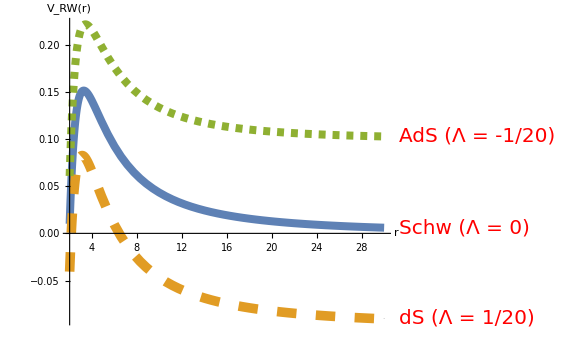

```mathematica
M=1;
Plot[{VRWodd[r,2,0],VRWodd[r,2,1/20],VRWodd[r,2,-1/20]},{r,Abs[rh[0.01]],30},PlotRange->All,AxesLabel->{"r","V_RW(r)"},AxesStyle->Directive[Red,20],LabelStyle->Directive[Red,20],Ticks->Automatic,TicksStyle->Directive[Pink,20],PlotStyle->{Thickness[0.010],{Dashing[Large],Thickness[0.012]},{Dashing[Small],Thickness[0.01]}},PlotLabels->Placed[{"Schw (Λ = 0)","dS (Λ = 1/20)","AdS (Λ = -1/20)"},Automatic],ImageSize->Large]
Clear[M]
```

### Zerilli equation

The evolution of even parity perturbations  is governed by the Zerilli equation. In its full glory, this is given by...

```mathematica
ZE//ColorOut
```

((432 M^4+l (1+l) (-2+l+l^2)^2 r^4 (-3+r^2 Λ)-72 M^3 r (9-3 l-3 l^2+r^2 Λ)+6 (-2+l+l^2)^2 M r^3 (-3+l+l^2+r^2 Λ)-12 M^2 r^2 (-30-6 l^3-3 l^4+2 r^4 Λ^2-3 l (-7+r^2 Λ)-3 l^2 (-6+r^2 Λ)))/(3 r^4 (6 M+(-2+l+l^2) r)^2)+ω^2) Kh[r_*[r]]+Kh''[r_*[r]]==(16 π (6 M-3 r+r^3 Λ) (-2 ⅈ r (18 M^2+(-2+l+l^2) r^4 Λ+3 M r (-4-l-l^2+4 r^2 Λ)) T_1[r_*[r]]-3 r^3 (6 M+(-2+l+l^2) r) ω T_2[r_*[r]]+108 M^2 r^2 ω T_G[r_*[r]]-72 M r^3 ω T_G[r_*[r]]+36 l M r^3 ω T_G[r_*[r]]+36 l^2 M r^3 ω T_G[r_*[r]]+12 r^4 ω T_G[r_*[r]]-12 l r^4 ω T_G[r_*[r]]-9 l^2 r^4 ω T_G[r_*[r]]+6 l^3 r^4 ω T_G[r_*[r]]+3 l^4 r^4 ω T_G[r_*[r]]-72 ⅈ M^2 t_0[r_*[r]]+48 ⅈ M r t_0[r_*[r]]-6 ⅈ l M r t_0[r_*[r]]-6 ⅈ l^2 M r t_0[r_*[r]]+6 ⅈ l r^2 t_0[r_*[r]]+3 ⅈ l^2 r^2 t_0[r_*[r]]-6 ⅈ l^3 r^2 t_0[r_*[r]]-3 ⅈ l^4 r^2 t_0[r_*[r]]-48 ⅈ M r^3 Λ t_0[r_*[r]]+8 ⅈ r^4 Λ t_0[r_*[r]]-4 ⅈ l r^4 Λ t_0[r_*[r]]-4 ⅈ l^2 r^4 Λ t_0[r_*[r]]+72 M^2 r ω t_1[r_*[r]]-60 M r^2 ω t_1[r_*[r]]+12 l M r^2 ω t_1[r_*[r]]+12 l^2 M r^2 ω t_1[r_*[r]]+12 r^3 ω t_1[r_*[r]]-6 l r^3 ω t_1[r_*[r]]-6 l^2 r^3 ω t_1[r_*[r]]+12 M r^4 Λ ω t_1[r_*[r]]-4 r^5 Λ ω t_1[r_*[r]]+2 l r^5 Λ ω t_1[r_*[r]]+2 l^2 r^5 Λ ω t_1[r_*[r]]+18 ⅈ M r^3 T_1'[r_*[r]]-6 ⅈ r^4 T_1'[r_*[r]]+3 ⅈ l r^4 T_1'[r_*[r]]+3 ⅈ l^2 r^4 T_1'[r_*[r]]+36 ⅈ M r^2 t_0'[r_*[r]]-12 ⅈ r^3 t_0'[r_*[r]]+6 ⅈ l r^3 t_0'[r_*[r]]+6 ⅈ l^2 r^3 t_0'[r_*[r]]))/(9 r^2 (6 M+(-2+l+l^2) r)^2 ω)

The potential for this is given by...

```mathematica
VZEeven[r_,l_,Λ_]=(VZE/.σ->((l-1)(l+2))/2//Simplify)//Evaluate;

"V"==VZEeven[r,l,Λ]//ColorOut
```

V==-(((6 M-3 r+r^3 Λ) (72 M^3+6 (-2+l+l^2)^2 M r^2+l (1+l) (-2+l+l^2)^2 r^3-12 M^2 r (6-3 l-3 l^2+2 r^2 Λ)))/(3 r^4 (6 M+(-2+l+l^2) r)^2))

For the dominant l=2 mode, here is a picture of the potential for the three cases: (i) Schwarzschild [Λ=0]; (ii) Schwarzschild-de Sitter [Λ>0]; (iii) Schwarzschild-anti de Sitter [Λ<0].

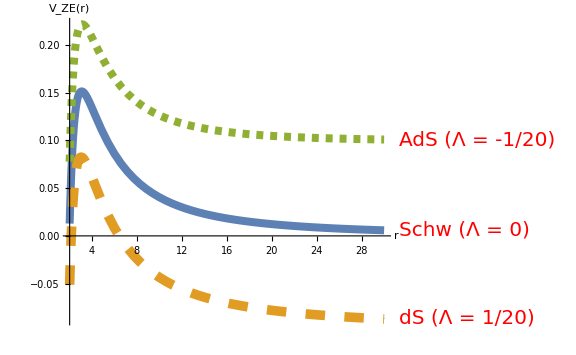

```mathematica
M=1;
Plot[{VZEeven[r,2,0],VZEeven[r,2,1/20],VZEeven[r,2,-1/20]},{r,Re[rh[0.01]],30},PlotRange->All,AxesLabel->{"r","V_ZE(r)"},AxesStyle->Directive[Red,20],LabelStyle->Directive[Red,20],Ticks->Automatic,TicksStyle->Directive[Pink,20],PlotStyle->{Thickness[0.010],{Dashing[Large],Thickness[0.012]},{Dashing[Small],Thickness[0.01]}},PlotLabels->Placed[{"Schw (Λ = 0)","dS (Λ = 1/20)","AdS (Λ = -1/20)"},Automatic],ImageSize->Large]
Clear[M]
```

## Gauge transformations

In this section, we assess the feasibility of choosing the RW gauge in analyzing the perturbations. To to this, we define a gauge vector (same order as perturbations) and its components.

As in the analysis of gravitational perturbations, it is useful to break down what follows into odd and even parts.

### Odd parity

For odd parity, the nongauge fixed odd parity perturbations are given by...

```mathematica
DefScalarFunction[h2,PrintAs->"h_2"];
oddfull=ϵ {{0,0,(-h0[r[]])/Sin[θ[]] D[YLM,ϕ[]],h0[r[]]Sin[θ[]] D[YLM,θ[]]},{0,0,(-h1[r[]])/Sin[θ[]] D[YLM,ϕ[]],h1[r[]]Sin[θ[]] D[YLM,θ[]]},{(-h0[r[]])/Sin[θ[]] D[YLM,ϕ[]],(-h1[r[]])/Sin[θ[]] D[YLM,ϕ[]],h2[r[]](1/Sin[θ[]] D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]]^2 D[YLM,ϕ[]]),1/2 h2[r[]](1/Sin[θ[]] D[YLM,{ϕ[],2}]+Cos[θ[]]D[YLM,θ[]]-Sin[θ[]]D[YLM,{θ[],2}])},{h0[r[]]Sin[θ[]] D[YLM,θ[]],h1[r[]]Sin[θ[]] D[YLM,θ[]],1/2 h2[r[]](1/Sin[θ[]] D[YLM,{ϕ[],2}]+Cos[θ[]]D[YLM,θ[]]-Sin[θ[]]D[YLM,{θ[],2}]),-h2[r[]](Sin[θ[]]D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]D[YLM,ϕ[]])}};
"h_ab"==(oddfull//MatrixForm)//ColorOut
```

h_ab==(0 | 0 | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] Sin[θ] P_lm'[θ])/(2 √π)
0 | 0 | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] Sin[θ] P_lm'[θ])/(2 √π)
(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π) | (ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π) | ϵ h_2[r] ((ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Cot[θ] Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)-(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm'[θ])/(2 √π)) | 1/2 ϵ h_2[r] (-(ⅇ^(-ⅈ ω t-ⅈ m ϕ) m^2 Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)+(ⅇ^(-ⅈ ω t-ⅈ m ϕ) Cos[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm'[θ])/(2 √π)-(ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] ((-l (1+l)+m^2 Csc[θ]^2) P_lm[θ]-Cot[θ] P_lm'[θ]))/(2 √π))
(ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] Sin[θ] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] Sin[θ] P_lm'[θ])/(2 √π) | 1/2 ϵ h_2[r] (-(ⅇ^(-ⅈ ω t-ⅈ m ϕ) m^2 Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)+(ⅇ^(-ⅈ ω t-ⅈ m ϕ) Cos[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm'[θ])/(2 √π)-(ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] ((-l (1+l)+m^2 Csc[θ]^2) P_lm[θ]-Cot[θ] P_lm'[θ]))/(2 √π)) | -ϵ h_2[r] ((ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Cos[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)-(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] P_lm'[θ])/(2 √π)))

We then define oddfull as components of the tensor h_ab...

```mathematica
DefTensor[Odd[-b,-c],Md,Symmetric[{-b,-c}],PrintAs->"h^(o)"];
ComponentValue[ComponentArray[Odd[-{b,Schw},-{c,Schw}]],oddfull];
```

For the gauge vector ζ, the odd parity components are given by

```mathematica
(*odd parity gauge vector*)
DefTensor[ζ[-a],Md]; 
DefScalarFunction[G];
ComponentValue[ComponentArray[ζ[{a,Schw}]],ϵ{0,0,-G[r[]]/(r[]^2 Sin[θ[]])D[YLM,ϕ[]],G[r[]]/(r[]^2 Sin[θ[]])D[YLM,θ[]]}];
ChangeComponents[ζ[-{a,Schw}],ζ[{a,Schw}]];
```

Computed ζ |  
a→g |   |  
b | a ζ | b
  in 0.0617315 Seconds

The perturbations, of course, transform as follows in a gauge transformation:

```mathematica
δhodd=(CD[-a][ζ[-b]]+CD[-b][ζ[-a]]);
"δh_bc"==δhodd//ColorOut

(*odd parity components of the gauge transformation*)
δhoddcomp=δhodd//ToBasis[Schw]//ToBasis[Schw]//TraceBasisDummy//ComponentArray//ToValues//ToValues//linearize;
```

δh_bc==▽_a ζ |  
b+▽_b ζ |  
a

We show that the angular pieces can be made to vanish. The odd parity perturbations become...

```mathematica
hnewodd=oddfull+δhoddcomp;
θθodd=hnewodd[[3,3]]//Simplify;
θφodd=hnewodd[[3,4]]//Simplify;
φφodd=hnewodd[[4,4]]//Simplify;

"h_33'"==θθodd//ColorOut
"h_34'"==θφodd//ColorOut
"h_44'"==φφodd//ColorOut
```

h_33'==-(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) (2 G[r]-h_2[r]) (Cot[θ] P_lm[θ]-P_lm'[θ]))/(2 √π)

h_34'==-1/(4 √π)ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (2 G[r]-h_2[r]) Sin[θ] ((l+l^2-2 m^2 Csc[θ]^2) P_lm[θ]+2 Cot[θ] P_lm'[θ])

h_44'==(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (2 G[r]-h_2[r]) (Cos[θ] P_lm[θ]-Sin[θ] P_lm'[θ]))/(2 √π)

Obviously the gauge choice 2G(r)-h_2(r)=0 picks up the Regge-Wheeler gauge for odd parity perturbations.

```mathematica
RWgaugeOdd=Solve[θθodd==0,h2[r[]]][[1]];

"h_2(r)"==h2[r[]]/.RWgaugeOdd//ColorOut
```

h_2(r)==2 G[r]

The perturbations finally take the form...

```mathematica
hRWodd=hnewodd/.RWgaugeOdd//Simplify;

NewPertFuncsOdd=Solve[{-2 G[r]+r (Subscript[h, 1][r]+G'[r])==α[r[]],-ⅈ ω G[r]+Subscript[h, 0][r]==β[r[]]},{Subscript[h, 0][r],Subscript[h, 1][r]}][[1]];

"h_ab"==(hRWodd/.NewPertFuncsOdd//Simplify//MatrixForm)//ColorOut
```

h_ab==(0 | 0 | (ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] β[r])/(2 √π) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] β[r] P_lm'[θ])/(2 √π)
0 | 0 | (ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] α[r])/(2 √π r) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] α[r] P_lm'[θ])/(2 √π r)
(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] β[r])/(2 √π) | (ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ Csc[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] α[r])/(2 √π r) | 0 | 0
(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] β[r] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] α[r] P_lm'[θ])/(2 √π r) | 0 | 0)

### Exercises

9. Is there a guage with h_0(r)=0? If yes, then what is the gauge vector G(r)?

10. Is there a guage with h_1(r)=0? If yes, then what is the gauge vector G(r)?

11. For the monopole (l=0,m=0), what happens to the odd parity h_ab?

## Gauge transformations

We continue our analysis of gauge transformations of the gravitational perturbations.

### Even parity

As in the analysis of metric perturbations, the even parity sector demands more work as more equations/components are involved.

First off, we define the even parity metric perturbations and its components in arbitrary gauge.

```mathematica
Clear[H2];
DefScalarFunction[H2,PrintAs->"H_2"];

DefScalarFunction[GG,PrintAs->"G"];
evenfull=ϵ {{h[r[]]H0[r[]]YLM,H1[r[]]YLM,h0[r[]] D[YLM,θ[]],h0[r[]] D[YLM,ϕ[]]},{H1[r[]]YLM,H2[r[]]/f[r[]] YLM,h1[r[]] D[YLM,θ[]],h1[r[]] D[YLM,ϕ[]]},{h0[r[]] D[YLM,θ[]],h1[r[]] D[YLM,θ[]],r[]^2(KK[r[]]YLM+GG[r[]]D[YLM,{θ[],2}]),r[]^2 GG[r[]](D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]] D[YLM,ϕ[]])},{h0[r[]] D[YLM,ϕ[]],h1[r[]] D[YLM,ϕ[]],r[]^2 GG[r[]](D[D[YLM,ϕ[]],θ[]]-Cos[θ[]]/Sin[θ[]] D[YLM,ϕ[]]),r[]^2(KK[r[]] Sin[θ[]]^2 YLM+GG[r[]](D[YLM,{ϕ[],2}]+Sin[θ[]]Cos[θ[]]D[YLM,θ[]]))}};
"h_ab"==(evenfull//MatrixForm)//ColorOut
```

h_ab==((ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h[r] H_0[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) H_1[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm'[θ])/(2 √π) | -(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π)
(ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) H_1[r] P_lm[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) H_2[r] P_lm[θ])/(2 √π f[r]) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm'[θ])/(2 √π) | -(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π)
(ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm'[θ])/(2 √π) | (ⅇ^(-ⅈ ω t-ⅈ m ϕ) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm'[θ])/(2 √π) | ϵ r^2 ((ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) K[r] P_lm[θ])/(2 √π)+(ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) G[r] ((-l (1+l)+m^2 Csc[θ]^2) P_lm[θ]-Cot[θ] P_lm'[θ]))/(2 √π)) | ϵ G[r] r^2 ((ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Cot[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)-(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m √(((1+2 l) (l-m)!)/((l+m)!)) P_lm'[θ])/(2 √π))
-(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_0[r] P_lm[θ])/(2 √π) | -(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h_1[r] P_lm[θ])/(2 √π) | ϵ G[r] r^2 ((ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m Cot[θ] √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)-(ⅈ ⅇ^(-ⅈ ω t-ⅈ m ϕ) m √(((1+2 l) (l-m)!)/((l+m)!)) P_lm'[θ])/(2 √π)) | ϵ r^2 ((ⅇ^(-ⅈ ω t-ⅈ m ϕ) √(((1+2 l) (l-m)!)/((l+m)!)) K[r] P_lm[θ] Sin[θ]^2)/(2 √π)+G[r] (-(ⅇ^(-ⅈ ω t-ⅈ m ϕ) m^2 √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ])/(2 √π)+(ⅇ^(-ⅈ ω t-ⅈ m ϕ) Cos[θ] √(((1+2 l) (l-m)!)/((l+m)!)) Sin[θ] P_lm'[θ])/(2 √π))))

We input this tensor into xCoba as follows.

```mathematica
DefTensor[Even[-b,-c],Md,Symmetric[{-b,-c}],PrintAs->"h^(e)"];
ComponentValue[ComponentArray[Even[-{b,Schw},-{c,Schw}]],evenfull];
```

We then define the even parity gauge vector ξ and its components.

```mathematica
(*even parity gauge vector*)
DefTensor[ξ[-a],Md]; 
DefScalarFunction[M0,PrintAs->"M_0"];
DefScalarFunction[M1,PrintAs->"M_1"];
DefScalarFunction[M2,PrintAs->"M_2"];
ComponentValue[ComponentArray[ξ[{a,Schw}]],ϵ{M0[r[]]YLM,M1[r[]]YLM,M2[r[]]D[YLM,θ[]],M2[r[]]/Sin[θ[]]^2 D[YLM,ϕ[]]}];
ChangeComponents[ξ[-{a,Schw}],ξ[{a,Schw}]];
```

Computed ξ |  
a→g |   |  
b | a ξ | b
  in 0.022939 Seconds

Finally, the gauge transformation of the even parity perturbations are computed in the next line.

```mathematica
δheven=(CD[-a][ξ[-b]]+CD[-b][ξ[-a]]);
"δh_bc"==δheven//ColorOut

(*odd parity components of the gauge transformation*)
δhevencomp=δheven//ToBasis[Schw]//ToBasis[Schw]//TraceBasisDummy//TraceBasisDummy//ComponentArray//ToValues//ToValues//linearize;
```

δh_bc==▽_a ξ |  
b+▽_b ξ |  
a

To reach the Regge-Wheeler gauge, the following components must vanish.

```mathematica
hneweven=evenfull+δhevencomp;
tθ=hneweven[[1,3]]//Simplify;
tφ=hneweven[[1,4]]//Simplify;
rθ=hneweven[[2,3]]//Simplify;
rφ=hneweven[[2,4]]//Simplify;
θφ=hneweven[[3,4]]//Simplify;

"h_13'"==tθ//ColorOut
"h_14'"==tφ//ColorOut
"h_23'"==rθ//ColorOut
"h_24'"==rφ//ColorOut
"h_34'"==θφ//ColorOut
```

h_13'==(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (h_0[r]-h[r] M_0[r]-ⅈ ω M_2[r] r^2) P_lm'[θ])/(2 √π)

h_14'==-(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] (h_0[r]-h[r] M_0[r]-ⅈ ω M_2[r] r^2))/(2 √π)

h_23'==(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (M_1[r]+f[r] (h_1[r]+r^2 M_2'[r])) P_lm'[θ])/(2 √π f[r])

h_24'==-(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] (M_1[r]+f[r] (h_1[r]+r^2 M_2'[r])))/(2 √π f[r])

h_34'==(ⅈ ⅇ^(-ⅈ (ω t+m ϕ)) m ϵ √(((1+2 l) (l-m)!)/((l+m)!)) (G[r]+2 M_2[r]) r^2 (Cot[θ] P_lm[θ]-P_lm'[θ]))/(2 √π)

Despite appearances, these components can be easily made to vanish. First, picking up M_2 from the θφ component, then M_1 from the rθ (or rφ) component, and lastly M_0 from the tθ (or tφ) component.

```mathematica
RWgaugeEven1=Solve[θφ==0,M2[r[]]][[1]];
RWgaugeEven1dM2={M2'[r[]]->D[M2[r[]]/.RWgaugeEven1,r[]]};
RWgaugeEven2=Solve[(rθ/.RWgaugeEven1dM2//Simplify)==0,M1[r[]]][[1]];
RWgaugeEven3=Solve[(tθ/.RWgaugeEven1//Simplify)==0,M0[r[]]][[1]];

(*to replace the first derivative*)
SimpD={M0'[r[]]->D[M0[r[]]/.RWgaugeEven3,r[]],M1'[r[]]->D[M1[r[]]/.RWgaugeEven2,r[]],M2'[r[]]->D[M2[r[]]/.RWgaugeEven1,r[]]};

RWgaugeEven=Union[RWgaugeEven1,RWgaugeEven2,RWgaugeEven1dM2,RWgaugeEven3,SimpD];

"M_2(r)"==M2[r[]]/.RWgaugeEven//ColorOut
"M_1(r)"==M1[r[]]/.RWgaugeEven//ColorOut
"M_0(r)"==M0[r[]]/.RWgaugeEven//ColorOut
```

M_2(r)==-G[r]/2

M_1(r)==-1/2 f[r] (2 h_1[r]-r^2 G'[r])

M_0(r)==(2 h_0[r]+ⅈ ω G[r] r^2)/(2 h[r])

The even parity perturbations then take the form...

```mathematica
hRWeven=hneweven/.RWgaugeEven//Simplify;

"h_ab"==(hRWeven//MatrixForm)//ColorOut
```

h_ab==(-(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] (-4 ⅈ ω h_0[r]-2 h[r] H_0[r]+2 ω^2 G[r] r^2-2 f[r] h_1[r] h'[r]+f[r] r^2 G'[r] h'[r]))/(4 √π) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] ((2 h_0[r]+ⅈ ω G[r] r^2) h'[r]+2 h[r] (ⅈ ω h_1[r]+H_1[r]-ⅈ ω G[r] r-ⅈ ω r^2 G'[r]-h_0'[r])))/(4 √π h[r]) | 0 | 0
(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] ((2 h_0[r]+ⅈ ω G[r] r^2) h'[r]+2 h[r] (ⅈ ω h_1[r]+H_1[r]-ⅈ ω G[r] r-ⅈ ω r^2 G'[r]-h_0'[r])))/(4 √π h[r]) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] (2 H_2[r]-2 h_1[r] f'[r]+4 f[r] r G'[r]+r^2 f'[r] G'[r]-4 f[r] h_1'[r]+2 f[r] r^2 G''[r]))/(4 √π f[r]) | 0 | 0
0 | 0 | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] r (K[r] r+f[r] (-2 h_1[r]+r^2 G'[r])))/(2 √π) | 0
0 | 0 | 0 | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] r Sin[θ]^2 (K[r] r+f[r] (-2 h_1[r]+r^2 G'[r])))/(2 √π))

Finally, we redefine the perturbations to obtain the final form of the even parity perturbations in RW gauge...

```mathematica
NewPertFuncsEven=Solve[{hRWeven[[1,1]]==(evenfull[[1,1]]/.H0[r[]]->Α[r[]]),hRWeven[[1,2]]==(evenfull[[1,2]]/.H1[r[]]->Β[r[]]),hRWeven[[2,2]]==(evenfull[[2,2]]/.H2[r[]]->Ζ[r[]]),hRWeven[[3,3]]==(evenfull[[3,3]]/.{KK[r[]]->Γ[r[]],GG[r[]]->0})},{H0[r[]],H1[r[]],H2[r[]],KK[r[]]}][[1]];

"h_ab"==(hRWeven/.NewPertFuncsEven//Simplify//MatrixForm)//ColorOut
```

h_ab==((ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) h[r] P_lm[θ] Α[r])/(2 √π) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] Β[r])/(2 √π) | 0 | 0
(ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] Β[r])/(2 √π) | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] Ζ[r])/(2 √π f[r]) | 0 | 0
0 | 0 | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] r^2 Γ[r])/(2 √π) | 0
0 | 0 | 0 | (ⅇ^(-ⅈ (ω t+m ϕ)) ϵ √(((1+2 l) (l-m)!)/((l+m)!)) P_lm[θ] r^2 Sin[θ]^2 Γ[r])/(2 √π))

### Exercises

12. Is it possible to have a gauge with h_1=K=G=0?

## Future work

Modern language (using gauge invariant master functions) is setup in Refs. [3,4].

[3] Martel, K. and Poisson, E., 2005. Gravitational perturbations of the Schwarzschild spacetime: A practical covariant and gauge-invariant formalism. Physical Review D, 71(10), p.104003.
[4] Nagar, A. and Rezzolla, L., 2005. Gauge-invariant non-spherical metric perturbations of Schwarzschild black-hole spacetimes. Classical and Quantum Gravity, 22(16), p.R167.

Here is a list of some possible future work (as of July 25 2019).

(1) GW templates. 
	The Regge-Wheeler and Zerilli equations are directly applicable to the calculation of gravitational waves from extreme mass-ratio inspirals (EMRIs) and the ringdown phase of binary black hole mergers.

(2) Gravitational perturbations in alternative theories, e.g., scalar-tensor theory. 
	Needless to say, the extension of the same perturbation analysis (even at linear order) is nontractable in alternative theories of gravity. This is a problem since it is desirable to compared the GW templates from GR and alternative theories. In scalar-tensor theory, the most rigorous analysis are presented in the following:

[5] Kobayashi, T., Motohashi, H. and Suyama, T., 2012. Black hole perturbation in the most general scalar-tensor theory with second-order field equations: The odd-parity sector. Physical Review D, 85(8), p.084025.

[6] Kobayashi, T., Motohashi, H. and Suyama, T., 2014. Black hole perturbation in the most general scalar-tensor theory with second-order field equations. II. The even-parity sector. Physical Review D, 89(8), p.084042.

(3) Perturbations in exotic objects.
	There should already be literature for the GWs for exotic objects such as wormholes. Nonetheless, the template banks for exotic objects in GR and, more so, in alternative theories may still be in premature development.

## Problems

#### Problem 1. Monopole perturbation

Obtain the exact solution to the perturbations in a Schwarzschild black hole for the case l=0. Find the gauge transformation (if it exists) that would lead to this solution.

#### Problem II. Dipolar perturbation: Odd parity

Obtain the exact solution to the odd parity vacuum perturbations in a Schwarzschild black hole for the case l=1. Find the gauge transformation (if it exists) that would lead to this solution.

#### Problem III. Dipolar perturbation: Even parity

Obtain the exact solution to the even parity vacuum perturbations in a Schwarzschild black hole for the case l=1. Find the gauge transformation (if it exists) that would lead to this solution.

#### Problem IV. Frame dragging: The slowly rotating metric

Consider a perturbation to the  tφ-component of the metric with the form Ω(r)sin^2(θ). Find the frame dragging function Ω(r) by solving the linearized Einstein equation.